# 改进的抛物线法作业

## 什么是数学实验：

数学实验是一种独特的数学研究与实践活动，它结合了理论思考与实践操作，旨在深入探索数学领域的未知奥秘。这一概念具有丰富的内涵，可以从多个维度进行理解和阐释。

首先，从广义的视角来看，数学实验是一种追求数学真理的探索过程。在这个过程中，实验者运用各种物质手段，如计算器、计算机等辅助工具，以及数学模型、算法等理论武器，通过数学思维的深度参与，在特定的实验环境中进行系统的数学研究。这些实验环境可以是现实的，也可以是虚拟的，但它们都为实验者提供了一个观察和检验数学现象、探索数学规律的舞台。通过这样的实验过程，实验者可以逐步揭示数学理论的内在逻辑，验证数学猜想的正确性，或者解决某个具体的数学问题。

其次，从更具体的层面来说，数学实验更多地依赖于计算机技术和数学软件的支持。这些先进的技术工具使得数学实验变得更加高效、精确和直观。通过数值计算，实验者可以对复杂的数学公式和算法进行快速求解；通过符号演算，可以探索数学表达式的变换规律和性质；通过图形显示，可以直观地呈现数学结果和规律，使得抽象的数学概念变得具象化、可视化。这些实践活动不仅有助于学生更好地理解和掌握数学知识，还能够激发他们的数学兴趣和创造力，培养他们的数学应用能力和创新能力。

## 对比基于泰勒中值定理的逼近模型构建&基于插值方法的逼近模型构建

## 1.基于泰勒中值定理的逼近模型构建是通过函数的局部导数信息来近似表示整个函数。泰勒定理表明，一个函数在某一点附近的值可以用该函数在该点的各阶导数值和对应的泰勒级数来表示。

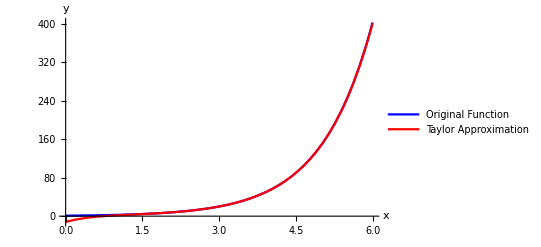

```mathematica
(*定义要逼近的函数*)f[x_]:=Exp[x];

(*定义泰勒逼近的阶数和逼近的中心点*)
order:=7;(*泰勒级数的阶数*)x0:=3.5;(*泰勒逼近的中心点*)(*使用泰勒中值定理创建逼近模型*)taylorApproximation=Series[f[x],{x,x0,order}];
normalFormApproximation=Normal[taylorApproximation];

(*绘制原函数和逼近多项式的图形对比*)
Plot[{f[x],normalFormApproximation},{x,0,6},PlotLegends->{"Original Function","Taylor Approximation"},PlotStyle->{Blue,Red},AxesLabel->{"x","y"}]
```

这种方法侧重于利用函数的局部性质，通过展开式来逼近函数的整体形态。其优点在于能够利用函数的导数信息，对于光滑函数具有较好的逼近效果；缺点在于需要计算高阶导数，计算量较大，且对于非光滑函数或存在奇异点的函数，逼近效果可能不佳。

## 2.基于插值方法的逼近模型构建则是通过一系列已知数据点来构造一个多项式或其他类型的函数，使其在这些数据点上的函数值与真实函数值相等或尽可能接近。

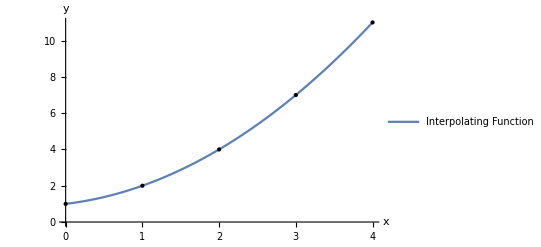

```mathematica
(*定义离散数据点*)data={{0,1},{1,2},{2,4},{3,7},{4,11}};

(*注意：这只适用于较小的数据集，因为插值多项式可能非常复杂*)
interpolatingPolynomial=InterpolatingPolynomial[data,x];

(*绘制原数据点和插值函数的图形对比*)
Plot[interpolatingPolynomial,{x,0,4},Epilog->{PointSize[Large],Point[data]},PlotLegends->{"Interpolating Function","Data Points"},(*在图上绘制原数据点*)AxesLabel->{"x","y"}]
```

插值方法强调对已知数据点的精确拟合，而不一定关注函数的导数信息。其优点在于能够直接利用离散数据点进行逼近，计算相对简单；缺点在于可能产生龙格现象（即在数据点之间的某些区域，插值函数可能出现较大的波动），且对于高维数据或复杂函数的插值问题，计算复杂度会显著增加。

## 3.联系

两种方法都是数学逼近理论的重要组成部分，都旨在通过已知信息来逼近未知函数。在实际应用中，可以根据问题的特点和需求灵活选择使用哪种方法。例如，对于光滑且导数易于计算的函数，可以考虑使用泰勒逼近；而对于离散数据点较多且关注数据点精确拟合的情况，插值方法可能更为合适。